```mathematica
datos =Import["Descargas/AvancesT/08_WehrlEntropyHP/Partition/Datos/64-65.dat"];
```

```mathematica
dat64 = datos[[;;70]];
dat65 = datos[[73;;142]];
```

```mathematica
list64  = Transpose[dat64];
list65 = Transpose[dat65];
```

```mathematica
Lista64 = Transpose[{list64[[1]],list64[[3]]}];
Lista65 = Transpose[{list65[[1]],list65[[3]]}];
```

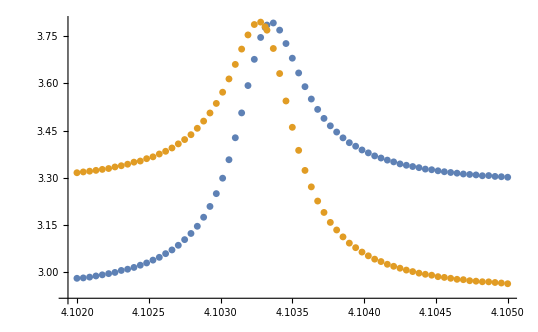

```mathematica
ListPlot[{Lista64,Lista65},PlotRange->All]
```

```mathematica
μ=4.10331;
```

```mathematica
Clear[x,σ,a]
```

```mathematica
model = 3.3 +a/(σ √(2Pi))Exp[(-(x-μ)^2)/(2 σ^2)];
```

```mathematica
FindFit[Lista64,model,{a,σ},x]
```

{a→0.000214238,σ→0.000180647}

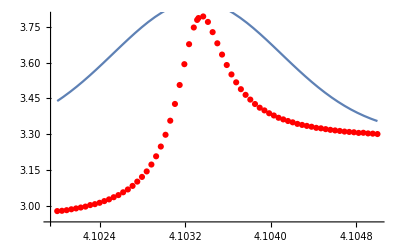

```mathematica
Show[ListPlot[Lista64,PlotStyle->Red],Plot[model/.{a->-0.0010967529339078648,σ->-0.0007870924014852},{x,4.102,4.105}]]
```